```mathematica
(*Import the first CSV file*)data1=Import["Updated Richters_Predictor_Modeling_Earthquake_Damage_-_Train_Values.csv"];

(*Import the second CSV file*)
data2=Import["Richters_Predictor_Modeling_Earthquake_Damage_-_Train_Labels.csv"];

(*data1 = data1[[;;10]];
data2 = data2[[;;10]];*)
```

```mathematica
Directory[]
```

/Users/prithvirajprabhu/Documents/Research projects local/CS 567 final project/Code/CS 567 final/Dataset

```mathematica
SetDirectory["/Users/prithvirajprabhu/Documents/Research projects local/CS 567 final project/Code/CS 567 final/Dataset"]
```

/Users/prithvirajprabhu/Documents/Research projects local/CS 567 final project/Code/CS 567 final/Dataset

```mathematica
(*Combine the two datasets*)
combinedData=Table[Join[data1[[j,2;;]],{data2[[j,2]]}],{j,2,Length@data1}];

(*Export the combined dataset to a new CSV file*)
Export["RPMED-Traincombined.csv",combinedData,"CSV"]
```

RPMED-Traincombined.csv

```mathematica
combinedData[[;;10]] //MatrixForm
```

(6 | 487 | 12198 | 2 | 30 | 6 | 5 | 3 | 3 | 1 | 1 | 2 | 4 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
8 | 900 | 2812 | 2 | 10 | 8 | 7 | 2 | 3 | 1 | 4 | 2 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
21 | 363 | 8973 | 2 | 10 | 5 | 5 | 3 | 3 | 1 | 1 | 4 | 4 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
22 | 418 | 10694 | 2 | 10 | 6 | 5 | 3 | 3 | 1 | 1 | 4 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
11 | 131 | 1488 | 3 | 30 | 8 | 9 | 3 | 3 | 1 | 1 | 4 | 3 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
8 | 558 | 6089 | 2 | 10 | 9 | 5 | 3 | 3 | 1 | 1 | 2 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
9 | 475 | 12066 | 2 | 25 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
20 | 323 | 12236 | 2 | 0 | 8 | 6 | 3 | 5 | 2 | 3 | 4 | 3 | 9 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 757 | 7219 | 2 | 15 | 8 | 6 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
26 | 886 | 994 | 1 | 0 | 13 | 4 | 3 | 2 | 1 | 3 | 1 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Dimensions@combinedData
```

{260601,39}

```mathematica
Position[combinedData,_String]
```

{{245880,14}}

```mathematica
combinedData //MatrixForm
```

(6 | 487 | 12198 | 2 | 30 | 6 | 5 | 3 | 3 | 1 | 1 | 2 | 4 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
8 | 900 | 2812 | 2 | 10 | 8 | 7 | 2 | 3 | 1 | 4 | 2 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
21 | 363 | 8973 | 2 | 10 | 5 | 5 | 3 | 3 | 1 | 1 | 4 | 4 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
22 | 418 | 10694 | 2 | 10 | 6 | 5 | 3 | 3 | 1 | 1 | 4 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
11 | 131 | 1488 | 3 | 30 | 8 | 9 | 3 | 3 | 1 | 1 | 4 | 3 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
8 | 558 | 6089 | 2 | 10 | 9 | 5 | 3 | 3 | 1 | 1 | 2 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
9 | 475 | 12066 | 2 | 25 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
20 | 323 | 12236 | 2 | 0 | 8 | 6 | 3 | 5 | 2 | 3 | 4 | 3 | 9 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 757 | 7219 | 2 | 15 | 8 | 6 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)

```mathematica
(*Import the first CSV file*)data1=Import["/Users/prithvirajprabhu/Documents/Research projects local/CS 567 final project/Code/CS 567 final/Dataset/RPMED-Traincombined.csv"];
```

```mathematica
data1[[;;10,{1,2,3,39}]] //mf
```

(6 | 487 | 12198 | 3
8 | 900 | 2812 | 2
21 | 363 | 8973 | 3
22 | 418 | 10694 | 2
11 | 131 | 1488 | 3
8 | 558 | 6089 | 2
9 | 475 | 12066 | 3
20 | 323 | 12236 | 1
0 | 757 | 7219 | 2
26 | 886 | 994 | 1)

Find the average damage level, or a tally for each id of the first feature.

```mathematica
maxf1 = Length@Sort@Tally@data1[[All,1]]
```

31

```mathematica
f1tallies = Table[{},maxf1];
Do[
AppendTo[f1tallies[[data1[[j,1]]+1]],data1[[j,Length@data1[[j]]]]]
,{j, Length@data1}];
Tally/@f1tallies
```

{{{2,3075},{1,337},{3,599}},{{2,1985},{3,305},{1,411}},{{1,85},{2,610},{3,236}},{{2,4550},{3,2745},{1,245}},{{2,11164},{3,2883},{1,521}},{{2,2014},{1,446},{3,230}},{{3,6051},{2,16222},{1,2108}},{{2,11273},{1,1033},{3,6688}},{{2,8513},{3,9913},{1,654}},{{3,664},{2,2733},{1,561}},{{2,12107},{3,8761},{1,1211}},{{3,3162},{2,4672},{1,386}},{{2,2310},{1,199},{3,685}},{{1,1966},{2,6275},{3,1367}},{{2,1247},{3,276},{1,191}},{{2,1673},{3,484},{1,163}},{{2,3188},{3,944},{1,200}},{{3,17615},{2,3913},{1,285}},{{3,2331},{2,786},{1,72}},{{3,66},{2,263},{1,43}},{{1,3311},{2,11860},{3,2045}},{{3,8710},{1,322},{2,5857}},{{2,4624},{3,817},{1,811}},{{2,768},{1,72},{3,281}},{{2,908},{3,132},{1,270}},{{2,4384},{3,772},{1,468}},{{1,8028},{2,12645},{3,1942}},{{3,6060},{2,6007},{1,465}},{{3,108},{2,157}},{{2,349},{3,39},{1,8}},{{2,2127},{3,307},{1,252}}}

```mathematica
datasetentropy = N@Entropy@data1[[All,-1]]
```

0.912732

```mathematica
gid1entropies = Entropy[#]&/@f1tallies;
gid1entropies //N//mf
```

(0.695789
0.759139
0.843456
0.784004
0.643666
0.724892
0.828617
0.835527
0.815906
0.832133
0.855478
0.832244
0.737478
0.880324
0.77001
0.749305
0.699672
0.537518
0.65986
0.801353
0.826851
0.763574
0.753963
0.782255
0.810825
0.673653
0.903516
0.826051
0.675953
0.418448
0.654696)

```mathematica
Entropy[{1,1,1,1}] //N
```

0.

## Decision tree algorithm

```mathematica
(*Define a function to calculate the entropy of a list of probabilities*)
entropy[prob_List]:=-Total[If[#==0,0,#*Log2[#]]&/@prob]

(*Define a function to calculate the information gain of a split*)
infoGain[labels_List,data_List,split_Integer]:=Module[{splitData=GatherBy[data,#[[split]]&],labelCounts,totalEntropy,subEntropies},
labelCounts=Tally[labels];
totalEntropy=entropy[(#[[2]]/Length[data])&/@labelCounts];
subEntropies=entropy[(#[[2]]/Length[data])&/@Tally[#[[All,1]]]]&/@splitData;
totalEntropy-Total[(Length[splitData[[#]]]/Length[data])*subEntropies[[#]]&/@Range[Length@subEntropies]]]

(*Define a recursive function to build the decision tree*)
decisionTree[labels_List,data_List,attributes_List]:=Module[{bestSplit,children,node, dataLabels = Table[{data[[i]], labels[[i]]},{i, Length@data}]},
(*Base case:all labels are the same*)If[Length[Tally[labels]]==1,Return[First[labels]]];
(*Base case:no attributes left to split on*)If[Length[attributes]==0,Return[First[Commonest[labels]]]];
(*Find the best attribute to split on*)bestSplit=Ordering[infoGain[labels,data,#]&/@Range[Length[attributes]],-1][[1]]; 
(*Create a node for the decision tree*)node=<|"Attribute"->attributes[[bestSplit]],"Children"-><||>|>;

(*Recursively build the decision tree for each child node*)
children=GatherBy[dataLabels,#[[bestSplit]]&];
Map[(node["Children"][#1]=decisionTree[#1[[All,2]],#1[[All,1,Complement[Range[Length[attributes]],{bestSplit}]]],Complement[attributes,{attributes[[bestSplit]]}]];)&,children];
Return[node]]
```

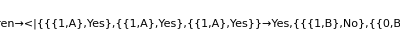

```mathematica
(*Example usage*)
data={{1,"A"},{1,"A"},{1,"A"},{1,"B"},{0,"B"},{0,"B"}};
attributes={"Feature 1","Feature 2"};
labels={"Yes","Yes","Yes","No","No","No"};

tree=decisionTree[labels,data,attributes];
tree//TreeForm
```

```mathematica
data={{1,"A","C"},{1,"A","C"},{1,"B","C"},{0,"B","C"},{0,"B","C"}};
attributes={"Feature 1","Feature 2","Feature 3"};
labels={"Yes","Yes","No","No","No"};

tree=decisionTree[labels,data,attributes];
tree
```

<|Attribute→Feature 2,Children→<|{{{1,A,C},Yes},{{1,A,C},Yes}}→Yes,{{{1,B,C},No},{{0,B,C},No},{{0,B,C},No}}→No|>|>

```mathematica
data={{1,"A"},{1,"A"},{1,"B"},{0,"B"},{0,"B"}};
attributes={"Feature 1","Feature 2"};
labels={"Yes","Yes","Yes","No","No"};

tree=decisionTree[labels,data,attributes];
tree
```

<|Attribute→Feature 2,Children→<|{{{1,A},Yes},{{1,A},Yes},{{1,B},Yes}}→Yes,{{{0,B},No},{{0,B},No}}→No|>|>

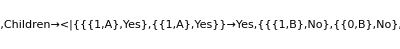

```mathematica
TreeForm@tree
```

```mathematica
(square[#1] = #1^2;)&,{2,3}
```

Syntax::tsntxi: "(square[#1]=#1^2;)&,{2,3}" is incomplete; more input is needed.

Part::partd: Part specification children⟦1⟧ is longer than depth of object.

children⟦1⟧

<|Attribute→Feature 2,Children→<||>|>

{{{{1,A},Yes},{{1,A},Yes}},{{{1,B},No},{{0,B},No},{{0,B},No}}}

{{{1,A},Yes},{{1,A},Yes},{{1,B},No},{{0,B},No},{{0,B},No}}

{2}

2

{{{1,A},Yes},{{1,A},Yes},{{1,B},No},{{0,B},No},{{0,B},No}}

{{{{1,A},Yes},{{1,A},Yes}},{{{1,B},No},{{0,B},No},{{0,B},No}}}

<|Attribute→Feature 2,Children→<||>|>

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[(node$25838660[Children][#1]=decisionTree[Tally[Part[«3»]]⟦All,1⟧,#1⟦All,Complement[Range[«1»],{«1»}]⟧,Complement[{Feature 1,Feature 2},{Part[«2»]}]];)&,{{{{1,A},Yes},{{1,A},Yes}},{{{1,B},No},{{0,B},No},{{0,B},No}}}]; dimensions are 2 and 3.

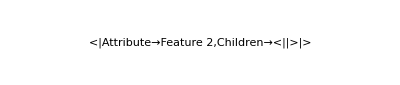

```mathematica
children[[1]]
```

```mathematica
MapThread[(node["Children"][#1]=decisionTree[#1[[All,2]],#1[[All,1,Complement[Range[Length[attributes]],{bestSplit}]]],Complement[attributes,{attributes[[bestSplit]]}]];)&,children];
```

```mathematica
childsren ={{{{1,"A"},"Yes"},{{1,"A"},"Yes"}},{{{1,"B"},"No"},{{0,"B"},"No"},{{0,"B"},"No"}}};
childs = childsren[[1]];
childs[[All,1,Complement[Range[Length[attributes]],{2}]]]
childs[[All,2]]
```

{{1},{1}}

{Yes,Yes}

```mathematica
Ordering[infoGain[labels,data,#]&/@Range[Length[attributes]],-1]
```

{{(3 Log[5/3])/(5 Log[2]),(2 Log[5/2])/(5 Log[2])},(3 Log[5/3])/(5 Log[2])+(2 Log[5/2])/(5 Log[2])}

{{(2 Log[5/2])/(5 Log[2]),(2 Log[5/2])/(5 Log[2])+Log[5]/(5 Log[2])},(3 Log[5/3])/(5 Log[2])+(2 Log[5/2])/(5 Log[2])}

{2}

```mathematica
infoGain[labels,data,1]
```

{{(3 Log[5/3])/(5 Log[2]),(2 Log[5/2])/(5 Log[2])},(3 Log[5/3])/(5 Log[2])+(2 Log[5/2])/(5 Log[2])}

(6 Log[5/3])/(25 Log[2])+(6 Log[5/2])/(25 Log[2])